```mathematica
Nd-LSCO 0.25 electron-like
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
dir=SetDirectory[NotebookDirectory[]]
direct=dir;
```

C:\Users\Brad\Documents\Visual Studio 2017\Projects\ConsoleApplication1\ConsoleApplication1

```mathematica
ℏ=1.05*10^-34;
e=1.6*10^-19;
m0=9.1*10^-31;
kB=1.38*10^-23;
jtoev=6.242*10^18;

c=13.2/2;
a =5.3/Sqrt[2];
b=5.3/Sqrt[2];

v [f_]:=(9.1*10^-31)10^-20/(10^-12)*1/ℏ{D[f,kx],D[f,ky],D[f,kz]};
kf[F_]:=Sqrt[(F 2Pi (e/(1.6*10^-19))/(ℏ/(9.1*10^-31)*10^20) (1/10^-12))/Pi];
ty= 1.6*10^-22 * 1/(9.1*10^-31) 1/(10^-10)^2 10^-24;
ftotal=(1.05*10^-34)(2Pi/(a*10^-10))^2 / (2 Pi *1.6*10^-19);

cdevs=5;
ϕdevs=40;
tdevs=500;
θmax=90;
θmin=0;
θdevs=45;

hopping={.215,.250,-.034,(-.034)*(-.5),.23}; (*good, from Johan*)
e0={475};
txpy={525};
txy={-60};
t2xp2y={16};
tz={9};
tz2={.5};
tauN={.5};
ϕdepτ={1};
power={8};


hopping=Flatten[Table[{atauN,ae0,atxpy,atxy,at2xp2y,atz,atz2,aϕdepτ,apower},{atauN,tauN},{ae0,e0},{atxpy,txpy},{atxy,txy},{at2xp2y,t2xp2y},{atz,tz},{atz2,tz2},{aϕdepτ,ϕdepτ},{apower,power}],8];

thetas = Table[θ,{θ,θmin*Pi/180,θmax*Pi/180.,(θmax-θmin)*Pi/180./θdevs}];
phis = {0.*Pi/180};

int=1;
ϵ[kx_,ky_,kz_,t_]:=   500t-500 2t (Cos[kx a]+Cos[ky a ])-+2 t*.01Cos[kz c/2]
energy=ϵ[kx,ky,kz,ty];
velocity01=Simplify[v[energy]];
velocityz01=velocity01[[3]];
kf001 = FindRoot[ϵ[0,ky,0,ty]==0,{ky,.8}][[1,2]];
velz01[kx_,ky_,kz_]=velocityz01;

kf0 = FindRoot[ϵ[0,ky,0,ty]==0,{ky,.7}][[1,2]];
Show[DensityPlot[Evaluate[velocityz]/.kz->-.5 Pi/(2 * 11.68),{kx,-1Pi/a,1Pi/a},{ky,-1Pi/b,1Pi/b},PlotLegends->Automatic,FrameLabel->{"x","y"}],ContourPlot[(efun/.kz->0)==0,{kx,-1Pi/a,1Pi/a},{ky,-1Pi/b,1Pi/b}]]
```

-Graphics-

```mathematica
f[kx_?NumericQ,ky_?NumericQ]:=efun/.kz->0 
area=NIntegrate[Boole[f[kx,ky]>= 0],{kx,-Pi/a,Pi/a},{ky,-Pi/a,Pi/a}];
ftotal=(1.05*10^-34)(2Pi/(a*10^-10))^2 / (2 Pi *1.6*10^-19);
atotal= (2Pi/a)(2Pi/b);
per = area/atotal
freq=per*ftotal
doping=per*2-1
```

NIntegrate::inumr: The integrand Boole[f[kx,ky]≥0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.83828,0.83828},{-0.83828,0.83828}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.355764 NIntegrate[Boole[f[kx,ky]≥0],{kx,-π/a,π/a},{ky,-π/a,π/a}]

NIntegrate::inumr: The integrand Boole[f[kx,ky]≥0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.83828,0.83828},{-0.83828,0.83828}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

10444.5 NIntegrate[Boole[f[kx,ky]≥0],{kx,-π/a,π/a},{ky,-π/a,π/a}]

NIntegrate::inumr: The integrand Boole[f[kx,ky]≥0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.83828,0.83828},{-0.83828,0.83828}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-1+0.711528 NIntegrate[Boole[f[kx,ky]≥0],{kx,-π/a,π/a},{ky,-π/a,π/a}]

```mathematica
num=24;
phi1=Table[{ArcTan[8.i/num],Sqrt[(i)^2.+(num/8)^2]},{i,0,num/8}];
phi2=Transpose[{Pi/2-Reverse[phi1[[All,1]]],Reverse[phi1[[All,2]]]}];
phi3=Transpose[{Pi-Reverse[phi2[[All,1]]],phi1[[All,2]]}];
phi4=Transpose[{3Pi/2-Reverse[phi3[[All,1]]],Reverse[phi1[[All,2]]]}];
phi5=Transpose[{4Pi/2-Reverse[phi4[[All,1]]],phi1[[All,2]]}];
phi6=Transpose[{5Pi/2-Reverse[phi5[[All,1]]],phi1[[All,2]]//Reverse}];
phi7=Transpose[{6Pi/2-Reverse[phi6[[All,1]]],phi1[[All,2]]}];
phi8=Transpose[{7Pi/2-Reverse[phi7[[All,1]]],phi1[[All,2]]//Reverse}];phispecial=((Join[phi1,phi2,phi3,phi4,phi5,phi6,phi7,phi8])[[All,1]]//DeleteDuplicates)+Pi/4;

Bfield=45.*1.6*10^-19 * 10^-12/(9.1*10^-31);
angles = Table[θ,{θ,θmin*Pi/180,θmax*Pi/180.,(θmax-θmin)*Pi/180./θdevs}];
phis = {0.*Pi/180};
```

```mathematica
Do[

τfun[px_,py_,τ0_,γ_]:=1/(1/τ0+γ(Sin[ArcTan[px,py]]^2-Cos[ArcTan[px,py]]^2)^hopping[[numbTimes,9]]);

ϵ01[kx_,ky_,kz_,t_]:=    500t-500 2t (Cos[kx a]+Cos[ky a ])-+2 t*.01Cos[kz c/2];




efun01=ϵ01[kx,ky,kz,ty];
velocity01=Simplify[v[efun01]];
velocityz01=velocity01[[3]];
  kf001 = FindRoot[ϵ01[0,ky,0,ty]==0,{ky,.8}][[1,2]];
velz01[kx_,ky_,kz_]=velocityz01;

 (*start01=Flatten[Table[Table[{FindRoot[(efun01/.kx->r Cos[θ]/.ky->r Sin[θ])==ef001,{r,kf001 }][[1,2]]Cos[θ],FindRoot[(efun01/.kx->r Cos[θ]/.ky->r Sin[θ])==ef001,{r,kf001 }][[1,2]]Sin[θ],kz},{θ,.01,2Pi,2.Pi/ϕdevs}],{kz,-2Pi/c,2Pi/c,4.Pi/c /cdevs}],1];*)

start01=Flatten[Table[Table[{FindRoot[(efun01/.kx->r Cos[θ]/.ky->r Sin[θ])==0,{r,.8 }][[1,2]]Cos[θ],FindRoot[(efun01/.kx->r Cos[θ]/.ky->r Sin[θ])==0,{r,.8 }][[1,2]]Sin[θ],kz},{θ,phispecial}],{kz,-2Pi/c,2Pi/c,4.Pi/c /cdevs}],1];

numGrid01 = Length[start01];
cond01= Table[Table[{0,0,0},{Length[angles]}],{Length[phis]}];

circ01=Plus@@Table[Sqrt[(start01[[i,1]]-start01[[i-1,1]])^2+(start01[[i,2]]-start01[[i-1,2]])^2],{i,2,Length[start01]}];

tnum = 8;

Module[{angleIndex,phiIndex,gridIndex,B = {0,0,1},state01,state11,state21,solution01=Table[Null,{Length[start01]}],Dx01,Dy01,Dz01,τ=hopping[[numbTimes,1]],τt=tnum*hopping[[numbTimes,1]],τs=tnum*hopping[[numbTimes,1]]/tdevs,times=Range[-tnum*hopping[[numbTimes,1]],0,tnum*hopping[[numbTimes,1]]/tdevs],Vz01,Vz11,Vz21,Exps},

For[phiIndex = 1, phiIndex≤ Length[phis],phiIndex++,
For[angleIndex = 1, angleIndex ≤ Length[angles],angleIndex++,
B = {Bfield*Sin[angles[[angleIndex]]]Cos[phis[[phiIndex]]],Bfield*Sin[angles[[angleIndex]]]Sin[phis[[phiIndex]]],Bfield*Cos[angles[[angleIndex]]]};

cond01[[phiIndex,angleIndex]]={phis[[phiIndex]]*180./Pi,angles[[angleIndex]]*180./Pi,0};

state01=First@NDSolve`ProcessEquations[{(11538.5)kx'[t] == -(1)Cross[velocity01/.kx->kx[t]/.ky->ky[t]/.kz->kz[t],B][[1]],(11538.5)ky'[t] == -(1)Cross[velocity01/.kx->kx[t]/.ky->ky[t]/.kz->kz[t],B][[2]],(11538.5)kz'[t] == -(1)Cross[velocity01/.kx->kx[t]/.ky->ky[t]/.kz->kz[t],B][[3]],kx[0] ==  start01[[1,1]],ky[0] ==  start01[[1,2]],kz[0] ==  start01[[1,3]]},{kx,ky,kz},t];

For[p1=1,p1≤ Length[start01],p1++, NDSolve`Iterate[state01,-hopping[[numbTimes,1]]*(tnum+1)]; solution01[[p1]]=NDSolve`ProcessSolutions[state01];state01=First@NDSolve`Reinitialize[state01,{kx[0] ==  start01[[p1,1]],ky[0] ==  start01[[p1,2]],kz[0] ==  start01[[p1,3]]}]];

Dx01=Evaluate[D[efun01,kx]];
Dy01=Evaluate[D[efun01,ky]];
Dz01=Evaluate[D[efun01,kz]];

For[gridIndex = 1,gridIndex≤ numGrid01,gridIndex++,

Vz01=velz01[solution01[[gridIndex,1,2]][times],solution01[[gridIndex,2,2]][times],solution01[[gridIndex,3,2]][times]];
taus=τfun[solution01[[gridIndex,1,2]][times],solution01[[gridIndex,2,2]][times],hopping[[numbTimes,1]],hopping[[numbTimes,8]]];
Exps=Exp[times/hopping[[numbTimes,1]]]*τs*10^-12;

cond01[[phiIndex,angleIndex,3]] += (1/Sqrt[(Dx01/.kx->solution01[[gridIndex,1,2]][0]/.ky->solution01[[gridIndex,2,2]][0]/.kz->solution01[[gridIndex,3,2]][0])^2 +(Dy01/.kx->solution01[[gridIndex,1,2]][0]/.ky->solution01[[gridIndex,2,2]][0]/.kz->solution01[[gridIndex,3,2]][0])^2+(Dz01/.kx->solution01[[gridIndex,1,2]][0]/.ky->solution01[[gridIndex,2,2]][0]/.kz->solution01[[gridIndex,3,2]][0])^2])*
((circ01 * 2Pi/c)/numGrid01)*(velocity01[[3]]/.kx->solution01[[gridIndex,1,2]][0]/.ky->solution01[[gridIndex,2,2]][0]/.kz
->solution01[[gridIndex,3,2]][0] )*
(Total[Vz01*Exps]);
];


];
];
];


str01=StringJoin[direct,"\\Calculations\\Nd_LSCO_0p25_tauN_",ToString[hopping[[numbTimes,1]]],"__e0_",ToString[hopping[[numbTimes,2]]],"__txpy_",ToString[hopping[[numbTimes,3]]],"__txy_",ToString[hopping[[numbTimes,4]]],"__t2xp2y_",ToString[hopping[[numbTimes,5]]],"__tz_",ToString[hopping[[numbTimes,6]]],"__tz2_",ToString[hopping[[numbTimes,7]]],"__tau2_",ToString[hopping[[numbTimes,8]]],"__power_",ToString[hopping[[numbTimes,9]]],".dat"];
Export[str01,Flatten[cond01,1]];

,{numbTimes,Length[hopping]}
]
```

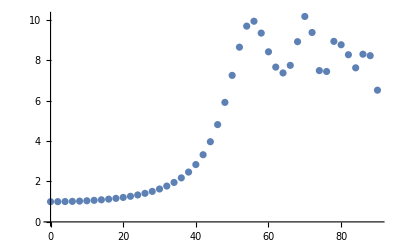

```mathematica
filenames=StringJoin[direct,"\\Calculations\\Nd_LSCO_0p25_tauN_",ToString[hopping[[#,1]]],"__e0_",ToString[hopping[[#,2]]],"__txpy_",ToString[hopping[[#,3]]],"__txy_",ToString[hopping[[#,4]]],"__t2xp2y_",ToString[hopping[[#,5]]],"__tz_",ToString[hopping[[#,6]]],"__tz2_",ToString[hopping[[#,7]]],"__tau2_",ToString[hopping[[#,8]]],"__power_",ToString[hopping[[#,9]]],".dat"]&/@Range[Length[hopping]];
conductivity=Import[#]&/@filenames;
contab=Table[Table[Select[conductivity[[j]],#1[[1]]==(180*phis[[i]])/Pi&],{i,1,Length[phis]}],{j,1,Length[conductivity]}];

con01Test=Table[Table[Select[Table[{contab[[k,j,i,2]],contab[[k,j,i,3]]/((9.1*10^-31)10^-30 1/((1.6*10^-19)^2/(4Pi^3)))},{i,1,Length[contab[[k,j]]]}],#[[1]]<=maxT&],{j,1,Length[contab[[k]]]}],{k,1,Length[contab]}];
res01=Table[Table[Table[{con01Test[[k,i,j,1]],(1/con01Test[[k,i,j,2]])/(0+1/con01Test[[k,i,1,2]])},{j,1,Length[con01Test[[k,i]]]}],{i,1,Length[con01Test[[k]]]}],{k,1,Length[con01Test]}];
ListPlot[res01[[1]]]
```

```mathematica
cond=Import["conductivity.dat"];
```

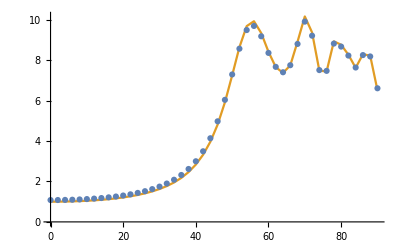

```mathematica
ListPlot[{Transpose[{cond[[All,1]]*180/Pi,1/cond[[All,2]]*(.55*10^-16)}],res01[[1,1]]},Joined->{False,True},PlotRange->All]
```